```mathematica
(*QuEST VQD Setup*)
Import["https://qtechtheory.org/questlink.m"]
CreateDownloadedQuESTEnv[];
Get["C:\\Users\\KitKa\\QuantumVolume\\QuESTCheck\\VQD CG V3 Parallel.wl"]
data=Import["SU4Gates9Qubits.csv"];
```

URLDownload::invhttp: Failed writing body (0 != 16384).

```mathematica
distloc[q1_, q2_] := 
			Norm[RydDev[AtomLocations][q1] - RydDev[AtomLocations][q2], 2] RydDev[UnitLattice];

blockadecheck[q_List] := 
			And @@ ((distloc @@ # <= (RydDev[BlockadeRadius]+$MachineEpsilon))& /@ Subsets[Flatten[q], {2}]);
```

```mathematica
(*VQD Initialisation*)locations=Association[#1->#2&@@@Transpose@{Range[0,8],{{0,0,0},{0,1,0},{1,0,0},{1,1,0},{0,2,0},{1,2,0},{2,0,0},{2,1,0},{2,2,0}}}];
SWAPlocations=Association[#1->#2&@@@Transpose@{Range[0,8],{{0,0,0},{0,1,0},{1,0,0},{1,1,0},{2,0,0},{2,1,0},{3,0,0},{3,1,0},{4,0,0}}}];
ParallelConfig={
(* The total number of atoms/qubit*)
QubitNum ->  9
,
(*Physical location on each qubit described with a 2D- or 3D-vector*)
AtomLocations -> SWAPlocations
,
(* It's presumed that Subscript[T, 2]^* has been echoed out to Subscript[T, 2] *)
T2 -> 1.49*10^6
,
(* The life time of vacuum chamber, where it affects the coherence time: T1=τvac/N  *)
VacLifeTime -> 4*10^6
,
(* Rabi frequency of the atoms. We assume the duration of multi-qubit gates is as long as 4π pulse of single-qubit gates *)
RabiFreq -> 1
,
(* Asymmetric bit-flip error probability; the error is acquired during single qubit operation *)
ProbBFRot -> <|10->0, 01->0|>
,
(* Unit lattice in μm. This will be the unit the lattice and coordinates *)
UnitLattice -> 1
,
(* blockade radius of each atom *)
BlockadeRadius -> 10
,
(* The factor that estimates accelerated dephasing due to moving the atoms. Ideally, it is calculated from the distance and speed. *)
HeatFactor -> 0
,
(* Leakage probability during initalisation process *)
ProbLeakInit -> 0.003(*0.007*)
,
(* duration of moving atoms; we assume SWAPLoc and ShiftLoc take this amount of time: 100 μs *)
DurMove -> 100
,
(* duration of lattice initialization which involves the atom loading (~50%) and rearranging the optical tweezer *)
DurInit -> 300
,
(* measurement fidelity and duration, were it induces atom loss afterward *)
FidMeas -> 100
,
DurMeas -> 2*10^4
,
(* The increasing probability of atom loss on each measurement. The value keeps increasing until being initialised *)
ProbLossMeas -> 0
,
(* leak probability of implementing multi-qubit gates *)
ProbLeakCZ -> <|01-> 0.001,11->0.001 |>
};
SWAPConfig={
(* The total number of atoms/qubit*)
QubitNum ->  9
,
(*Physical location on each qubit described with a 2D- or 3D-vector*)
AtomLocations -> SWAPlocations
,
(* It's presumed that Subscript[T, 2]^* has been echoed out to Subscript[T, 2] *)
T2 -> 1.49*10^6
,
(* The life time of vacuum chamber, where it affects the coherence time: T1=τvac/N  *)
VacLifeTime -> 4*10^6
,
(* Rabi frequency of the atoms. We assume the duration of multi-qubit gates is as long as 4π pulse of single-qubit gates *)
RabiFreq -> 1
,
(* Asymmetric bit-flip error probability; the error is acquired during single qubit operation *)
ProbBFRot -> <|10->0, 01->0|>
,
(* Unit lattice in μm. This will be the unit the lattice and coordinates *)
UnitLattice -> 1
,
(* blockade radius of each atom *)
BlockadeRadius -> 1.1
,
(* The factor that estimates accelerated dephasing due to moving the atoms. Ideally, it is calculated from the distance and speed. *)
HeatFactor -> 0
,
(* Leakage probability during initalisation process *)
ProbLeakInit -> 0.003(*0.007*)
,
(* duration of moving atoms; we assume SWAPLoc and ShiftLoc take this amount of time: 100 μs *)
DurMove -> 0
,
(* duration of lattice initialization which involves the atom loading (~50%) and rearranging the optical tweezer *)
DurInit -> 300
,
(* measurement fidelity and duration, were it induces atom loss afterward *)
FidMeas -> 100
,
DurMeas -> 2*10^4
,
(* The increasing probability of atom loss on each measurement. The value keeps increasing until being initialised *)
ProbLossMeas -> 0
,
(* leak probability of implementing multi-qubit gates *)
ProbLeakCZ -> <|01-> 0.001,11->0.001 |>
};
MoveTime=100
Options[RydbergHub]=ParallelConfig;
RydDev=RydbergHub[];
PlotAtoms[RydbergHub[]]
```

100

-Graphics3D-

```mathematica
(*Algorithm to determine the necessary operations for any two qubits to share connection*)
(*By "Rail" we mean they are colinear along the x-axis of the grid*)
SWAPSchedulePI[GateData_,A_,B_,LocTrackerPI_]:=Module[
{},
LocTracker=LocTrackerPI;
Which[
(*Same Rail*)

EvenQ[Abs[LocTracker[[A+1]]-LocTracker[[B+1]]]],
(*Print["Same Rail"];*)
If[
LocTracker[[A+1]]==LocTracker[[B+1]]+2||LocTracker[[A+1]]==LocTracker[[B+1]]-2,
{LocTracker,Flatten[{SU4GateDCPI[GateData,A,B]}]},
MaxPosi=Max[{LocTracker[[A+1]],LocTracker[[B+1]]}];
MinPosi=Min[{LocTracker[[A+1]],LocTracker[[B+1]]}];
MaxPosQi=Flatten[Position[LocTracker,MaxPosi]][[1]]-1;
li=(MaxPosi-MinPosi)/2-1;
(*Print["m= ",li];*)
OutputLayer=Flatten[Join[
Table[
MaxPos=Max[{LocTracker[[A+1]],LocTracker[[B+1]]}];
MaxPosQ=Flatten[Position[LocTracker,MaxPos]][[1]]-1;
MinPos=Min[{LocTracker[[A+1]],LocTracker[[B+1]]}];
(*Print["MaxPos ",MaxPos," MinPos ",MinPos, " MaxPosQ ",MaxPosQ ];*)
MoveTarg=Flatten[Position[LocTracker,MaxPos-2]][[1]]-1;
LocTracker[[Flatten[Position[LocTracker,MaxPos-2]][[1]]]]+=2;
LocTracker[[MaxPosQ+1]]-=2;
{Subscript[SWAPDCPIRL, MaxPosQi,MoveTarg],Subscript[SWAPLoc, MoveTarg,MaxPosQi]},
{i,1,li}],
{SU4GateDCPI[GateData,A,B]}]];
(*Print["LocTracker",LocTracker];*)
{LocTracker,OutputLayer}
],

(*Different rail, A is the top rail*)
OddQ[LocTracker[[A+1]]],
(*Print["A odd, Diff Rail"];*)
Which[
(*Aligned*)
LocTracker[[A+1]]==LocTracker[[B+1]]+1,
(*Print["Aligned"];*)
{LocTracker,Flatten[{SU4GateDCPI[GateData,A,B]}]},
(*A Right of B*)
LocTracker[[A+1]]>LocTracker[[B+1]],
(*Print["A RHS B"];*)
m=(LocTracker[[A+1]]-(LocTracker[[B+1]]+1))/2;
OutputLayer=Flatten[Join[
Table[
MoveTarg=Flatten[Position[LocTracker,LocTracker[[A+1]]-2]][[1]]-1;
LocTracker[[Flatten[Position[LocTracker,LocTracker[[A+1]]-2]][[1]]]]+=2;
LocTracker[[A+1]]-=2;
(*Print["Desired SWAP: " ,A, " -> ", MoveTarg];*)
{Subscript[SWAPDCPIRL, MoveTarg,A],Subscript[SWAPLoc, MoveTarg,A]},
{i,1,m}],
{SU4GateDCPI[GateData,A,B]}]];
(*Print["LocTracker",LocTracker];*)
{LocTracker,OutputLayer},
(*A left of B*)


LocTracker[[A+1]]<LocTracker[[B+1]],
(*Print["A LHS B"];*)
m=(LocTracker[[B+1]]-(LocTracker[[A+1]]-1))/2;

OutputLayer=Flatten[Join[
Table[
(*Print["LocTracker Before ", LocTracker];*)
MoveTarg=Flatten[Position[LocTracker,LocTracker[[B+1]]-2]][[1]]-1;
LocTracker[[Flatten[Position[LocTracker,LocTracker[[B+1]]-2]][[1]]]]+=2;
LocTracker[[B+1]]-=2;
(*Print["Desired SWAP: " , B, " -> ", MoveTarg];
Print["LocTracker After ", LocTracker];*)
{Subscript[SWAPDCPIRL, MoveTarg,B],Subscript[SWAPLoc, MoveTarg,B]},
{i,1,m}],
{SU4GateDCPI[GateData,A,B]}]];
(*Print["LocTracker",LocTracker];*)
{LocTracker,OutputLayer}
],


(*Different rail, B is the top rail*)
OddQ[LocTracker[[ B+1]]],
(*Print["Diff Rail, B top"];*)
Which[
(*Aligned*)

LocTracker[[A+1]]==LocTracker[[B+1]]-1,
(*Print["Aligned"];*)
{LocTracker,Flatten[{SU4GateDCPI[GateData,A,B]}]},
(*A right of B*)

LocTracker[[A+1]]>LocTracker[[B+1]],
(*Print["A RHS B"];*)
m=(LocTracker[[A+1]]-(LocTracker[[B+1]]-1))/2;
OutputLayer=Flatten[Join[
Table[
MoveTarg=Flatten[Position[LocTracker,LocTracker[[A+1]]-2]][[1]]-1;
LocTracker[[Flatten[Position[LocTracker,LocTracker[[A+1]]-2]][[1]]]]+=2;
LocTracker[[A+1]]-=2;
(*Print["Desired SWAP: " , A, " -> ", MoveTarg];*)
{Subscript[SWAPDCPIRL, MoveTarg,A],Subscript[SWAPLoc, MoveTarg,A]},{i,1,m}],
{SU4GateDCPI[GateData,A,B]}]];
(*Print["LocTracker",LocTracker];*)
{LocTracker,OutputLayer},
(*A Left of B*)

LocTracker[[A+1]]<LocTracker[[B+1]],
(*Print["A LHS B"];*)
m=(LocTracker[[B+1]]-(LocTracker[[A+1]]+1))/2;
OutputLayer=Flatten[Join[
Table[
MoveTarg=Flatten[Position[LocTracker,LocTracker[[B+1]]-2]][[1]]-1;
LocTracker[[Flatten[Position[LocTracker,LocTracker[[B+1]]-2]][[1]]]]+=2;
LocTracker[[B+1]]-=2;
(*Print["Desired SWAP: " ,B , " -> ", MoveTarg];*)
{Subscript[SWAPDCPIRL, MoveTarg,B],Subscript[SWAPLoc, MoveTarg,B]},{i,1,m}],
{SU4GateDCPI[GateData,A,B]}]];
(*Print["LocTracker",LocTracker];*)
{LocTracker,OutputLayer}
]
]]
```

```mathematica
(*Algorithm to determine the necessary operations for any two qubits to share connection*)
(*By "Rail" we mean they are colinear along the x-axis of the grid*)
SWAPScheduleARP[GateData_,A_,B_,LocTrackerARP_]:=Module[
{},
LocTracker=LocTrackerARP;
Which[
(*Same Rail*)

EvenQ[Abs[LocTracker[[A+1]]-LocTracker[[B+1]]]],
(*Print["Same Rail"];*)
If[
LocTracker[[A+1]]==LocTracker[[B+1]]+2||LocTracker[[A+1]]==LocTracker[[B+1]]-2,
{LocTracker,Flatten[{SU4GateDCARP[GateData,A,B]}]},
MaxPosi=Max[{LocTracker[[A+1]],LocTracker[[B+1]]}];
MinPosi=Min[{LocTracker[[A+1]],LocTracker[[B+1]]}];
MaxPosQi=Flatten[Position[LocTracker,MaxPosi]][[1]]-1;
li=(MaxPosi-MinPosi)/2-1;
(*Print["m= ",li];*)
OutputLayer=Flatten[Join[
Table[
MaxPos=Max[{LocTracker[[A+1]],LocTracker[[B+1]]}];
MaxPosQ=Flatten[Position[LocTracker,MaxPos]][[1]]-1;
MinPos=Min[{LocTracker[[A+1]],LocTracker[[B+1]]}];
(*Print["MaxPos ",MaxPos," MinPos ",MinPos, " MaxPosQ ",MaxPosQ ];*)
MoveTarg=Flatten[Position[LocTracker,MaxPos-2]][[1]]-1;
LocTracker[[Flatten[Position[LocTracker,MaxPos-2]][[1]]]]+=2;
LocTracker[[MaxPosQ+1]]-=2;
{Subscript[SWAPDCARPRL, MaxPosQi,MoveTarg],Subscript[SWAPLoc, MoveTarg,MaxPosQi]},
{i,1,li}],
{SU4GateDCARP[GateData,A,B]}]];
(*Print["LocTracker",LocTracker];*)
{LocTracker,OutputLayer}
],

(*Different rail, A is the top rail*)
OddQ[LocTracker[[A+1]]],
(*Print["A odd, Diff Rail"];*)
Which[
(*Aligned*)
LocTracker[[A+1]]==LocTracker[[B+1]]+1,
(*Print["Aligned"];*)
{LocTracker,Flatten[{SU4GateDCARP[GateData,A,B]}]},
(*A Right of B*)
LocTracker[[A+1]]>LocTracker[[B+1]],
(*Print["A RHS B"];*)
m=(LocTracker[[A+1]]-(LocTracker[[B+1]]+1))/2;
OutputLayer=Flatten[Join[
Table[
MoveTarg=Flatten[Position[LocTracker,LocTracker[[A+1]]-2]][[1]]-1;
LocTracker[[Flatten[Position[LocTracker,LocTracker[[A+1]]-2]][[1]]]]+=2;
LocTracker[[A+1]]-=2;
(*Print["Desired SWAP: " ,A, " -> ", MoveTarg];*)
{Subscript[SWAPDCARPRL, MoveTarg,A],Subscript[SWAPLoc, MoveTarg,A]},
{i,1,m}],
{SU4GateDCARP[GateData,A,B]}]];
(*Print["LocTracker",LocTracker];*)
{LocTracker,OutputLayer},
(*A left of B*)


LocTracker[[A+1]]<LocTracker[[B+1]],
(*Print["A LHS B"];*)
m=(LocTracker[[B+1]]-(LocTracker[[A+1]]-1))/2;

OutputLayer=Flatten[Join[
Table[
(*Print["LocTracker Before ", LocTracker];*)
MoveTarg=Flatten[Position[LocTracker,LocTracker[[B+1]]-2]][[1]]-1;
LocTracker[[Flatten[Position[LocTracker,LocTracker[[B+1]]-2]][[1]]]]+=2;
LocTracker[[B+1]]-=2;
(*Print["Desired SWAP: " , B, " -> ", MoveTarg];
Print["LocTracker After ", LocTracker];*)
{Subscript[SWAPDCARPRL, MoveTarg,B],Subscript[SWAPLoc, MoveTarg,B]},
{i,1,m}],
{SU4GateDCARP[GateData,A,B]}]];
(*Print["LocTracker",LocTracker];*)
{LocTracker,OutputLayer}
],


(*Different rail, B is the top rail*)
OddQ[LocTracker[[ B+1]]],
(*Print["Diff Rail, B top"];*)
Which[
(*Aligned*)

LocTracker[[A+1]]==LocTracker[[B+1]]-1,
(*Print["Aligned"];*)
{LocTracker,Flatten[{SU4GateDCARP[GateData,A,B]}]},
(*A right of B*)

LocTracker[[A+1]]>LocTracker[[B+1]],
(*Print["A RHS B"];*)
m=(LocTracker[[A+1]]-(LocTracker[[B+1]]-1))/2;
OutputLayer=Flatten[Join[
Table[
MoveTarg=Flatten[Position[LocTracker,LocTracker[[A+1]]-2]][[1]]-1;
LocTracker[[Flatten[Position[LocTracker,LocTracker[[A+1]]-2]][[1]]]]+=2;
LocTracker[[A+1]]-=2;
(*Print["Desired SWAP: " , A, " -> ", MoveTarg];*)
{Subscript[SWAPDCARPRL, MoveTarg,A],Subscript[SWAPLoc, MoveTarg,A]},{i,1,m}],
{SU4GateDCARP[GateData,A,B]}]];
(*Print["LocTracker",LocTracker];*)
{LocTracker,OutputLayer},
(*A Left of B*)

LocTracker[[A+1]]<LocTracker[[B+1]],
(*Print["A LHS B"];*)
m=(LocTracker[[B+1]]-(LocTracker[[A+1]]+1))/2;
OutputLayer=Flatten[Join[
Table[
MoveTarg=Flatten[Position[LocTracker,LocTracker[[B+1]]-2]][[1]]-1;
LocTracker[[Flatten[Position[LocTracker,LocTracker[[B+1]]-2]][[1]]]]+=2;
LocTracker[[B+1]]-=2;
(*Print["Desired SWAP: " ,B , " -> ", MoveTarg];*)
{Subscript[SWAPDCARPRL, MoveTarg,B],Subscript[SWAPLoc, MoveTarg,B]},{i,1,m}],
{SU4GateDCARP[GateData,A,B]}]];
(*Print["LocTracker",LocTracker];*)
{LocTracker,OutputLayer}
]
]]
```

```mathematica
(*Defining QuEST's Rydberg Blockade Check in a permanent function such that it can be used without constantly editing the code*)
LocTrack[Nq_]:=Range[0,Nq-1]
distloc[q1_,q2_]:=Norm[qubitLocs[q1]-qubitLocs[q2],2]*userconfig[UnitLattice];
blockadeCheck[q_List]:=And@@((distloc@@#<= userconfig[BlockadeRadius])&/@Subsets[Flatten[q],{2}]);
Fraction[a_,b_]:=a/b
KetList[NQ_]:=Table[i,{i,0,2^NQ-1,1}]
NRandQbits[NQ_,i_]:=If[i==0,Range[0,NQ-1],RandomSample[Range[0,NQ-1],NQ]]

(*Randomly generated list, each 2 qubits represent a randomly generated pair*)
QList={0,3,2,7,1,5,6,4,8};

(*Constructed list which replaces the qubit labels with their respective current grid position labels*)
QLoclist=Table[LocTrack[Length[QList]][[QList[[i]]+1]],{i,1,Length[QList]}]

(*Sort the qubit pairs in such a way that the pairs which require the least operations to connect are first in the schedule*)
(*RTN: Pair #, Seperation between qubits as indicator of how many operations needed to connect*)
GateOrdering=SortBy[Table[{i-Quotient[i,2],Abs[QLoclist[[i]]-QLoclist[[i+1]]]},{i,1,Length[QLoclist]-1,2}],Last][[All,1]]
RQSOrd=Flatten[Table[QList[[{2*GateOrdering[[i]]-1,2*GateOrdering[[i]]}]],{i,1,Length[GateOrdering]}]]

CheckHeavyOutputProb[PoutcomesIMPLEMENTED_,PoutcomesMODEL_]:=Pick[PoutcomesIMPLEMENTED,Table[If[PoutcomesMODEL[[i]]>=Median[PoutcomesMODEL],True,False],{i,1,Length[PoutcomesMODEL]}]];
```

{0,3,2,7,1,5,6,4,8}

{4,1,3,2}

{6,4,0,3,1,5,2,7}

```mathematica
SU4GateARPMove[DataSet_,q1_,q2_]:=SequenceSplit[Flatten[Table[a=Reverse[IntegerPart[ToExpression[StringSplit[StringTrim[StringSplit[DataSet[[i]],", ["][[2]],"]"],","]]]];
b=If[Length[a]==1,StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],StringSplit[StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],"C"][[1]]];
c=StringReplace[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[3]]],"]]"],{"("->"[",")"->"]"}];
c=If[StringContainsQ[c,"e"],d=StringSplit[c,"e"];
ToExpression[d[[1]]]*10^ToExpression[d[[2]]],ToExpression[c]];
a=ReplaceAll[a,{0->q1,1->q2}];
If[Length[a]==2,If[StringContainsQ[b,"SWAP"],Subscript[ToExpression[SWAP],a[[1]],a[[2]]],{TwoQ,Subscript[CZARPPar,a[[2]],a[[1]]],TwoQ}],If[c==={},Subscript[ToExpression[b],a[[1]]],Subscript[ToExpression[b],a[[1]]][c]]],{i,1,Length[DataSet]}]],{TwoQ}]
```

```mathematica
NQ=5
RQs={0,1,2,3,4}

(*Parallelised SU4 Gate layer generators*)
SU4GateARPParMove[DataSet_,q1_,q2_]:=SequenceSplit[Flatten[Table[a=Reverse[IntegerPart[ToExpression[StringSplit[StringTrim[StringSplit[DataSet[[i]],", ["][[2]],"]"],","]]]];
b=If[Length[a]==1,StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],StringSplit[StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],"C"][[1]]];
c=StringReplace[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[3]]],"]]"],{"("->"[",")"->"]"}];
c=If[StringContainsQ[c,"e"],d=StringSplit[c,"e"];
ToExpression[d[[1]]]*10^ToExpression[d[[2]]],ToExpression[c]];
a=ReplaceAll[a,{0->q1,1->q2}];
If[Length[a]==2,If[StringContainsQ[b,"SWAP"],Subscript[ToExpression[SWAP],a[[1]],a[[2]]],{TwoQ,Subscript[CZARPPar,a[[2]],a[[1]]],TwoQ}],If[c==={},Subscript[ToExpression[b],a[[1]]],Subscript[ToExpression[b],a[[1]]][c]]],{i,1,Length[DataSet]}]],{TwoQ}]

SU4GatePIParMove[DataSet_,q1_,q2_]:=SequenceSplit[Flatten[Table[a=Reverse[IntegerPart[ToExpression[StringSplit[StringTrim[StringSplit[DataSet[[i]],", ["][[2]],"]"],","]]]];
b=If[Length[a]==1,StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],StringSplit[StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],"C"][[1]]];
c=StringReplace[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[3]]],"]]"],{"("->"[",")"->"]"}];
c=If[StringContainsQ[c,"e"],d=StringSplit[c,"e"];
ToExpression[d[[1]]]*10^ToExpression[d[[2]]],ToExpression[c]];
a=ReplaceAll[a,{0->q1,1->q2}];
If[Length[a]==2,If[StringContainsQ[b,"SWAP"],Subscript[ToExpression[SWAP],a[[1]],a[[2]]],{TwoQ,Subscript[CZPIPar,a[[2]],a[[1]]],TwoQ}],If[c==={},Subscript[ToExpression[b],a[[1]]],Subscript[ToExpression[b],a[[1]]][c]]],{i,1,Length[DataSet]}]],{TwoQ}]

(*(*Fully Translate Qiskit output into QuEST format, SWAP Procedure, ARP CZ*)
SU4GateDCARP[DataSet_,q1_,q2_]:=Table[
a=Reverse[IntegerPart[ToExpression[StringSplit[StringTrim[StringSplit[DataSet[[i]],", ["][[2]],"]"],","]]]];b=If[Length[a]==1,StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],StringSplit[StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],"C"][[1]]];
c=StringReplace[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[3]]],"]]"],{"("->"[",")"->"]"}];
c=If[StringContainsQ[c,"e"],d=StringSplit[c,"e"];ToExpression[d[[1]]]*10^ToExpression[d[[2]]],ToExpression[c]];
a=ReplaceAll[a,{0->q1,1->q2}];
If[Length[a]==2,If[StringContainsQ[b,"SWAP"],Subscript[ToExpression[SWAPDCARP], a[[1]],a[[2]]],Subscript[CZARP, a[[2]],a[[1]]]],If[c==={},Subscript[ToExpression[b], a[[1]]],Subscript[ToExpression[b], a[[1]]][c]]],{i,1,Length[DataSet]}]
(*Fully Translate Qiskit output into QuEST format, SWAP Procedure, GA CZ*)

SU4GateDCPI[DataSet_,q1_,q2_]:=Table[
a=Reverse[IntegerPart[ToExpression[StringSplit[StringTrim[StringSplit[DataSet[[i]],", ["][[2]],"]"],","]]]];b=If[Length[a]==1,StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],StringSplit[StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],"C"][[1]]];
c=StringReplace[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[3]]],"]]"],{"("->"[",")"->"]"}];
c=If[StringContainsQ[c,"e"],d=StringSplit[c,"e"];ToExpression[d[[1]]]*10^ToExpression[d[[2]]],ToExpression[c]];
a=ReplaceAll[a,{0->q1,1->q2}];
If[Length[a]==2,If[StringContainsQ[b,"SWAP"],Subscript[ToExpression[SWAPDCPI], a[[1]],a[[2]]],Subscript[CZPI, a[[2]],a[[1]]]],If[c==={},Subscript[ToExpression[b], a[[1]]],Subscript[ToExpression[b], a[[1]]][c]]],{i,1,Length[DataSet]}]
*)
(*Parallelised SU4 Gate layer generators*)
SU4GateDCARP[DataSet_,q1_,q2_]:=SequenceSplit[Flatten[Table[a=Reverse[IntegerPart[ToExpression[StringSplit[StringTrim[StringSplit[DataSet[[i]],", ["][[2]],"]"],","]]]];
b=If[Length[a]==1,StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],StringSplit[StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],"C"][[1]]];
c=StringReplace[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[3]]],"]]"],{"("->"[",")"->"]"}];
c=If[StringContainsQ[c,"e"],d=StringSplit[c,"e"];
ToExpression[d[[1]]]*10^ToExpression[d[[2]]],ToExpression[c]];
a=ReplaceAll[a,{0->q1,1->q2}];
If[Length[a]==2,If[StringContainsQ[b,"SWAP"],Subscript[ToExpression[SWAP],a[[1]],a[[2]]],{TwoQ,Subscript[CZARP,a[[2]],a[[1]]],TwoQ}],If[c==={},Subscript[ToExpression[b],a[[1]]],Subscript[ToExpression[b],a[[1]]][c]]],{i,1,Length[DataSet]}]],{TwoQ}]

SU4GateDCPI[DataSet_,q1_,q2_]:=SequenceSplit[Flatten[Table[a=Reverse[IntegerPart[ToExpression[StringSplit[StringTrim[StringSplit[DataSet[[i]],", ["][[2]],"]"],","]]]];
b=If[Length[a]==1,StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],StringSplit[StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],"C"][[1]]];
c=StringReplace[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[3]]],"]]"],{"("->"[",")"->"]"}];
c=If[StringContainsQ[c,"e"],d=StringSplit[c,"e"];
ToExpression[d[[1]]]*10^ToExpression[d[[2]]],ToExpression[c]];
a=ReplaceAll[a,{0->q1,1->q2}];
If[Length[a]==2,If[StringContainsQ[b,"SWAP"],Subscript[ToExpression[SWAP],a[[1]],a[[2]]],{TwoQ,Subscript[CZPI,a[[2]],a[[1]]],TwoQ}],If[c==={},Subscript[ToExpression[b],a[[1]]],Subscript[ToExpression[b],a[[1]]][c]]],{i,1,Length[DataSet]}]],{TwoQ}]
```

5

{0,1,2,3,4}

```mathematica
QVLayerARPMove[DataSet_,NQ_,RQs_,i_]:=Join[Table[SU4GateARPMove[DataSet[[n-Quotient[n,2]+i]],RQs[[n]],RQs[[n+1]]],{n,1,2*Quotient[NQ,2],2}],2];

QVLayerPIMove[DataSet_,NQ_,RQs_,i_]:=
Join[Table[SU4GatePIMove[DataSet[[n-Quotient[n,2]+i]],RQs[[n]],RQs[[n+1]]],{n,1,2*Quotient[NQ,2],2}],2];


QVLayerARPParMove[DataSet_,NQ_,RQs_,i_]:=Flatten[Table[SU4S=Join[Table[SU4GateARPParMove[DataSet[[n-Quotient[n,2]+i]],RQs[[n]],RQs[[n+1]]],{n,1,2*Quotient[NQ,2],2}]];Join[If[OddQ[j],CircRydbergHub[Flatten[SU4S[[All,j]]],RydDev,Parallel->True],If[OddQ[NQ],{Flatten[Append[SU4S[[All,j]],{Subscript[SpareARP, RQs[[-1]]],Subscript[Wait, 0][MoveTime]}]]},{Flatten[SU4S[[All,j]]]}]]],{j,1,7}],1]

QVLayerPIParMove[DataSet_,NQ_,RQs_,i_]:=Flatten[Table[SU4S=Join[Table[SU4GatePIParMove[DataSet[[n-Quotient[n,2]+i]],RQs[[n]],RQs[[n+1]]],{n,1,2*Quotient[NQ,2],2}]];Join[If[OddQ[j],CircRydbergHub[Flatten[SU4S[[All,j]]],RydDev,Parallel->True],If[OddQ[NQ],{Flatten[Append[SU4S[[All,j]],{Subscript[SparePI, RQs[[-1]]],Subscript[Wait, 0][MoveTime]}]]},{Flatten[SU4S[[All,j]]]}]]],{j,1,7}],1];

QVLayerARPPropSWAP[DataSet_,NQ_,RQs_,i_,LocTracker_]:=
Module[{},LocTrackerARP=LocTracker ;Table[
QLoclist=Table[LocTrackerARP[[RQs[[j]]+1]],{j,1,NQ}];

GateOrdering=SortBy[Table[If[EvenQ[QLoclist[[j]]-QLoclist[[j+1]]]&& Abs[QLoclist[[j]]-QLoclist[[j+1]]]==2,{j-Quotient[j,2],0},{j-Quotient[j,2],Abs[QLoclist[[j]]-QLoclist[[j+1]]]}],{j,1,Length[QLoclist]-1,2}],Last][[All,1]];

RQSOrd=Flatten[Table[RQs[[{2*GateOrdering[[j]]-1,2*GateOrdering[[j]]}]],{j,1,Length[GateOrdering]}]];
OutSlice=SWAPScheduleARP[DataSet[[n-Quotient[n,2]+i]],RQSOrd[[n]],RQSOrd[[n+1]],LocTrackerARP];
LocTrackerARP=OutSlice[[1]];
OutSlice,
{n,1,2*Quotient[NQ,2],2}]]

QVLayerPIPropSWAP[DataSet_,NQ_,RQs_,i_,LocTracker_]:=
Module[{},LocTrackerPI=LocTracker ;Table[
QLoclist=Table[LocTrackerPI[[RQs[[j]]+1]],{j,1,NQ}];

GateOrdering=SortBy[Table[If[EvenQ[QLoclist[[j]]-QLoclist[[j+1]]]&& Abs[QLoclist[[j]]-QLoclist[[j+1]]]==2,{j-Quotient[j,2],0},{j-Quotient[j,2],Abs[QLoclist[[j]]-QLoclist[[j+1]]]}],{j,1,Length[QLoclist]-1,2}],Last][[All,1]];

RQSOrd=Flatten[Table[RQs[[{2*GateOrdering[[j]]-1,2*GateOrdering[[j]]}]],{j,1,Length[GateOrdering]}]];
OutSlice=SWAPSchedulePI[DataSet[[n-Quotient[n,2]+i]],RQSOrd[[n]],RQSOrd[[n+1]],LocTrackerPI];
LocTrackerPI=OutSlice[[1]];
OutSlice,
{n,1,2*Quotient[NQ,2],2}]]
```

```mathematica
InitCirc[Reg_,MaxNQ_]:=Table[Subscript[Init, b],{b,0,MaxNQ-1,1}]
```

```mathematica
(*Generate circuit of m=d layers of SU(4) gates*)
QVCirc[DataSet_,NQ_,ConnectivityRule_]:=Which[

StringContainsQ[ConnectivityRule,"ARPMove"],
Table[RQS=NRandQbits[NQ,i];QVLayerARPMove[DataSet,NQ,RQS,i],{i,0,NQ-1,1}],

StringContainsQ[ConnectivityRule,"PIMove"],
Table[RQS=NRandQbits[NQ,i];QVLayerPIMove[DataSet,NQ,RQS,i],{i,0,NQ-1,1}],

StringContainsQ[ConnectivityRule,"PIParMove"],
Flatten[Table[RQS=NRandQbits[NQ,i];QVLayerPIParMove[DataSet,NQ,RQS,i],{i,0,NQ-1,1}],1],

StringContainsQ[ConnectivityRule,"ARPParMove"],
Flatten[Table[RQS=NRandQbits[NQ,i];QVLayerARPParMove[DataSet,NQ,RQS,i],{i,0,NQ-1,1}],1],

StringContainsQ[ConnectivityRule,"PIPropSWAP"],
OutCirc=Flatten[Table[RQS=NRandQbits[NQ,i];If[i==0, LocTrac=Range[0,NQ-1]];
LocNCirc=QVLayerPIPropSWAP[DataSet,NQ,RQS,i,LocTrac];
LocTrac=LocNCirc[[-1,1]];
LocNCirc[[All,2]],{i,0,NQ-1,1}]];{OutCirc},

StringContainsQ[ConnectivityRule,"ARPPropSWAP"],
OutCirc=Flatten[Table[RQS=NRandQbits[NQ,i];If[i==0, LocTrac=Range[0,NQ-1]];
LocNCirc=QVLayerARPPropSWAP[DataSet,NQ,RQS,i,LocTrac];
LocTrac=LocNCirc[[-1,1]];
LocNCirc[[All,2]],{i,0,NQ-1,1}]
];
{OutCirc}]
```

```mathematica
(*Generating and applying the circuits to a register and getting the probability of a heavy output*)
(*Perfect renormalisation on a given circuit, unsure if this is best or if taking an average across the NCirc is a more "accurate" scheme*)
QVProcedure[DataSet_,NQ_, MaxNQ_,NReps_,Reg_,ConnectivityRule_]:=Table[
Circ1=QVCirc[DataSet[[NQ*Quotient[NQ,2]*Rep+1;;NQ*Quotient[NQ,2]*(Rep+1)]],NQ,ConnectivityRule];
Initialisation={InitCirc[Reg,MaxNQ]};
InitCircuit=Join[Initialisation,Circ1];
Which[StringContainsQ[ConnectivityRule,"SWAP"],Options[RydbergHub]=SWAPConfig;RydDev=RydbergHub[];InitCircuit=CircRydbergHub[Flatten[InitCircuit],RydDev,Parallel->True],StringContainsQ[ConnectivityRule,"Par"],Options[RydbergHub]=ParallelConfig;RydDev=RydbergHub[]];

(*Print[Circ1];*)
CircNoisy=ExtractCircuit[InsertCircuitNoise[InitCircuit,RydDev,ReplaceAliases->True]];
Which[StringContainsQ[ConnectivityRule,"SWAP"],Options[RydbergHub]=SWAPConfig;RydDev=RydbergHub[],StringContainsQ[ConnectivityRule,"Par"],Options[RydbergHub]=ParallelConfig;RydDev=RydbergHub[]];
CircModel=ExtractCircuit[GetCircuitSchedule[Circ1,RydDev,ReplaceAliases->True]];
(*Print[CircModel];*)
RandomMixState[Reg,9];
Which[StringContainsQ[ConnectivityRule,"SWAP"],Options[RydbergHub]=SWAPConfig;RydDev=RydbergHub[],StringContainsQ[ConnectivityRule,"Par"],Options[RydbergHub]=ParallelConfig;RydDev=RydbergHub[]];
ApplyCircuit[Reg,CircNoisy];
PoutcomesNoisy=CalcProbOfAllOutcomes[Reg,Range[0,NQ-1]];
(*Print[PoutcomesNoisy];*)
InitZeroState[Reg];
(*Print[DrawCircuit[CircModel]];*)
Which[StringContainsQ[ConnectivityRule,"SWAP"],Options[RydbergHub]=SWAPConfig;RydDev=RydbergHub[],StringContainsQ[ConnectivityRule,"Par"],Options[RydbergHub]=ParallelConfig;RydDev=RydbergHub[]];
ApplyCircuit[Reg,CircModel];
PoutcomesModel=CalcProbOfAllOutcomes[Reg,Range[0,NQ-1]];
PNoLoss=Total[PoutcomesNoisy];
PoutcomesNoisyRen=PoutcomesNoisy/PNoLoss;
(*Print[NQ, " Model Outcomes Probabilities ",PoutcomesModel," Noisy Outcome Probabilities ",PoutcomesNoisy];*)
HeavyOutputs=CheckHeavyOutputProb[PoutcomesNoisy,PoutcomesModel];
HeavyOutputsRen=CheckHeavyOutputProb[PoutcomesNoisyRen,PoutcomesModel];
{Total[HeavyOutputs],Total[HeavyOutputsRen],1-PNoLoss},{Rep,0,NReps-1,1}]
```

```mathematica
(*Put everything together and get a value for Quantum Volume*)
QVCalc[DataSet_,MaxNQ_,NReps_,ConnectivityRule_]:=Table[ρ=CreateDensityQureg[MaxNQ];
(*DataStart=(Total[Table[a*Quotient[a,2],{a,0,NQ-1}]]*NReps)+1;
DataEnd=Total[Table[a*Quotient[a,2],{a,0,NQ}]*NReps];
Print[NQ,"  ",DataStart,"  ",DataEnd];*)
HOP=QVProcedure[DSSplice=DataSet[[(Total[Table[a*Quotient[a,2],{a,0,NQ-1}]]*NReps)+1 ;;Total[Table[a*Quotient[a,2],{a,0,NQ}]*NReps]]],NQ,MaxNQ,NReps,ρ,ConnectivityRule];
DestroyAllQuregs[];
MHOP=Mean[HOP[[All,1]]];
MHOPRen=Mean[HOP[[All,2]]];
MPLoss=Mean[HOP[[All,3]]];
σPLoss=StandardDeviation[HOP[[All,3]]]/Sqrt[NReps-1];
σ=StandardDeviation[HOP[[All,1]]]/Sqrt[NReps-1];
σRen=StandardDeviation[HOP[[All,2]]]/Sqrt[NReps-1];
If[ Re[(MHOP-2σ)]>2/3,VQ=2^NQ,VQ=0];
If[ Re[(MHOPRen-2σRen)]>2/3,VQRen=2^NQ,VQRen=0];
Print[{"Layer",NQ,VQ,VQRen}];
{{NQ,MHOP,2σ},{NQ,MHOPRen,2σRen},{NQ,MPLoss,σPLoss}}
,{NQ,2,MaxNQ,1}];
```

```mathematica
GateCountUpTo[Nq_,NReps_]:=If[Nq==2,0,Total[Table[i*NReps*Quotient[i,2],{i,2,Nq-1}]]];

QVCalcCustOrder[DataSet_,MaxNQ_,NReps_,ConnectivityRule_,NQ_]:=Module[{},ρ=CreateDensityQureg[MaxNQ];
(*DataStart=(Total[Table[a*Quotient[a,2],{a,0,NQ-1}]]*NReps)+1;
DataEnd=Total[Table[a*Quotient[a,2],{a,0,NQ}]*NReps];
Print[NQ,"  ",DataStart,"  ",DataEnd];*)
HOP=QVProcedure[DSSplice=DataSet[[GateCountUpTo[NQ,NReps]+1 ;;GateCountUpTo[NQ+1,NReps]]],NQ,MaxNQ,NReps,ρ,ConnectivityRule];
DestroyAllQuregs[];
MHOP=Mean[HOP[[All,1]]];
MHOPRen=Mean[HOP[[All,2]]];
MPLoss=Mean[HOP[[All,3]]];
σPLoss=StandardDeviation[HOP[[All,3]]]/Sqrt[NReps-1];σ=StandardDeviation[HOP[[All,1]]]/Sqrt[NReps-1];
σRen=StandardDeviation[HOP[[All,2]]]/Sqrt[NReps-1];
If[ Re[(MHOP-2σ)]>2/3,VQ=2^NQ,VQ=0];
If[ Re[(MHOPRen-2σRen)]>2/3,VQRen=2^NQ,VQRen=0];
Print[{"Layer",NQ,VQ,VQRen}];
{{NQ,MHOP,2σ},{NQ,MHOPRen,2σRen},{NQ,MPLoss,σPLoss}}];
```

```mathematica
QVCalcCustOrder[data,9,20,"ARPParMove",3]
QVCalcCustOrder[data,9,20,"ARPParMove",5]
QVCalcCustOrder[data,9,20,"ARPParMove",6]
```

```mathematica
QVCalcCustOrder[data,9,20,"ARPPropSWAP",3]
QVCalcCustOrder[data,9,20,"ARPPropSWAP",5]
QVCalcCustOrder[data,9,20,"ARPPropSWAP",6]
```

{Layer,3,8,8}

{Layer,5,32,32}

{Layer,6,64,64}

```mathematica
QVCalcCustOrder[data,9,20,"PIParMove",3]
QVCalcCustOrder[data,9,20,"PIParMove",5]
QVCalcCustOrder[data,9,20,"PIParMove",6]
```

```mathematica
QVCalcCustOrder[data,9,20,"PIPropSWAP",3]
QVCalcCustOrder[data,9,20,"PIPropSWAP",5]
QVCalcCustOrder[data,9,20,"PIPropSWAP",6]
```

{Layer,3,8,8}

{Layer,5,32,32}

```mathematica
QVCalcCustOrder[data,9,20,"ARPParMove",2]
QVCalcCustOrder[data,9,20,"ARPParMove",4]
QVCalcCustOrder[data,9,20,"ARPParMove",7]
```

```mathematica
QVCalcCustOrder[data,9,20,"ARPPropSWAP",2]
QVCalcCustOrder[data,9,20,"ARPPropSWAP",4]
QVCalcCustOrder[data,9,20,"ARPPropSWAP",7]
```

{Layer,2,4,4}

{Layer,4,16,16}

{Layer,7,128,128}

```mathematica
QVCalcCustOrder[data,9,20,"PIParMove",2]
QVCalcCustOrder[data,9,20,"PIParMove",4]
QVCalcCustOrder[data,9,20,"PIParMove",7]
```

```mathematica
QVCalcCustOrder[data,9,20,"PIPropSWAP",2]
QVCalcCustOrder[data,9,20,"PIPropSWAP",4]
QVCalcCustOrder[data,9,20,"PIPropSWAP",7]
```

{Layer,2,4,4}

{Layer,4,16,16}

{Layer,7,128,128}

{Layer,4,16,16}

{Layer,7,128,128}

```mathematica
QVCalcCustOrder[data,9,20,"ARPParMove",8]
```

```mathematica
QVCalcCustOrder[data,9,20,"ARPPropSWAP",8]
```

{Layer,8,0,256}

```mathematica
QVCalcCustOrder[data,9,20,"PIParMove",8]
```

```mathematica
QVCalcCustOrder[data,9,20,"PIPropSWAP",8]
```

{Layer,8,256,256}

```mathematica
QVCalcCustOrder[data,9,20,"ARPParMove",9]
```

```mathematica
QVCalcCustOrder[data,9,20,"ARPPropSWAP",9]
```

{Layer,9,0,512}

```mathematica
QVCalcCustOrder[data,9,20,"PIParMove",9]
```

```mathematica
QVCalcCustOrder[data,9,20,"PIPropSWAP",9]
```

{Layer,9,0,512}

```mathematica
QVARPParMove20={{{2,0.7367170331320891,0.04046211543367366},{2,0.764749878073313,0.042225338027914734},{2,0.03659315927485268,0.00033216369754386274}},{{3,0.7972016147750783,0.037997717051979345},{3,0.8320761159501098,0.03942527321975315},{3,0.04196417663272828,0.0003127492087065543}},{{4,0.806565495993669,0.02813504544511576},{4,0.8634431830622752,0.030037585016467278},{4,0.06587579386363054,0.0005231919323347731}},{{5,0.8032841048353907,0.016816989491519437},{5,0.8694624115334812,0.01827071042810927},{5,0.07610418016441352,0.0006881505390703912}},{{6,0.7470195211114234,0.012188139337635993},{6,0.8430795265191329,0.013525008250521792},{6,0.1139510078937582,0.0007316851783764358}},{{7,0.7499480909652398,0.008178783244002464},{7,0.8564338314520656,0.009044735595449611},{7,0.12434733020453681,0.0005681903416947865}},{{8,0.7014438469584208,0.004308942142488813},{8,0.8482289329107724,0.005120782585438621},{8,0.1730465989718519,0.0006567944441522319}},{{9,0.6823963147304062,0.003890468668853473},{9,0.8417131726458701,0.004571511061075104},{9,0.18927866409391375,0.0005907905919117739}}};
```

```mathematica
QVPIParMove20={{{2,0.7730700650644117,0.04674012782204616},{2,0.7987067323350912,0.04824842732526719},{2,0.0321108335978688,0.00014940215909161537}},{{3,0.806244571944446,0.03451419263702706},{3,0.8352521366505299,0.035706143146150615},{3,0.034740445713732325,0.00014376102424644085}},{{4,0.7948402381087786,0.020124910064179588},{4,0.8351372237937685,0.021174404643865885},{4,0.04824757246878275,0.0002666510233577028}},{{5,0.7985296586581321,0.015519125682652766},{5,0.8444813586551799,0.016460145938480834},{5,0.05440943684513685,0.00023028407145060537}},{{6,0.7791195329740265,0.01217492437645163},{6,0.8433376898704387,0.013323612368791659},{6,0.07613579531438588,0.00023785542414443017}},{{7,0.7867272485952498,0.007419986029456256},{7,0.8578348057063081,0.008177131938335094},{7,0.08288713992562456,0.0002953443724454984}},{{8,0.7443269928742173,0.00632016516691577},{8,0.8374574243586466,0.006948914999640895},{8,0.1112118665781269,0.0003269333931920217}},{{9,0.735805167141057,0.004256508363986669},{9,0.8372012184831213,0.004830782148940504},{9,0.1211126149382371,0.00029314254495417145}}};
```

```mathematica
QVPIPropSWAP20={{{2,0.7561665445258635,0.04046177256962648},{2,0.7812986383807081,0.041808896826708415},{2,0.03216710767106391,0.00012389489804886419}},{{3,0.8047400872567121,0.042852318265413115},{3,0.8351610187583299,0.044384247196370796},{3,0.03643377771238498,0.0004827746433923927}},{{4,0.7949295671975305,0.018369234878714648},{4,0.8383524333665626,0.019243788461617894},{4,0.05180824046923962,0.0005174746192581158}},{{5,0.8104194676943086,0.01707497850767336},{5,0.8656659930851511,0.017839001676152048},{5,0.06384947795100422,0.0010974768593380823}},{{6,0.7583846159480634,0.012645735668571693},{6,0.8363898913396254,0.013492173905058061},{6,0.0932815448852845,0.0015138662634812902}},{{7,0.7517594896826454,0.010354353923481227},{7,0.8528200299894056,0.010818624208712598},{7,0.11850614155873976,0.0022494751709476062}},{{8,0.6842855078272254,0.006807139302557327},{8,0.8266186207170503,0.006605129349281135},{8,0.17220700156882274,0.0020258698785183414}},{{9,0.6401563860127399,0.009142692322219884},{9,0.8119067089345691,0.008383795801103027},{9,0.21160565807211212,0.0030638198138698467}}};

QVARPPropSWAP20={{{2,0.7573141706041507,0.05072844212535921},{2,0.7859767059094228,0.05267708517322304},{2,0.036461334030043965,0.0003109379862990574}},{{3,0.7897067393389127,0.024366676759534488},{3,0.8258626247004207,0.025297702251871463},{3,0.043794273901037475,0.0007506658261536305}},{{4,0.7789109669694222,0.02504875074226859},{4,0.8358718306131125,0.02683867778695384},{4,0.06814677740702606,0.0009111685008136299}},{{5,0.7702440567976647,0.010607618687384239},{5,0.8512613347788476,0.011694358888011323},{5,0.09514008287811868,0.0018396249410869766}},{{6,0.72125105371491,0.012029455009522632},{6,0.845457105966984,0.01368056281584734},{6,0.14688102041777767,0.0024088155680782888}},{{7,0.6876810472390341,0.007388458749822273},{7,0.8442861266003318,0.00707831073951992},{7,0.18543693560185334,0.003465956817650859}},{{8,0.6176476726935304,0.010653814738639869},{8,0.8374822394378046,0.008156586687502465},{8,0.2626014175698299,0.004429046684788672}},{{9,0.5710630842900535,0.010451951161870721},{9,0.8381065463839924,0.005690103943119903},{9,0.31871897398079446,0.005123879791720487}}};
```

```mathematica
IdealHOP=Table[{i,(1+Log[2])/2},{i,2,9}];
Thresh=Table[{i,2/3},{i,2,9}];
```

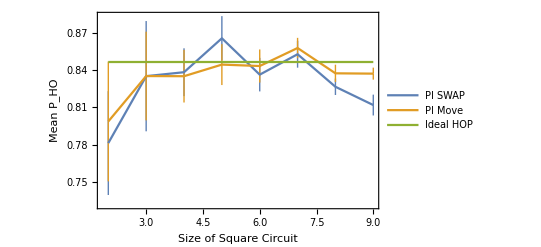

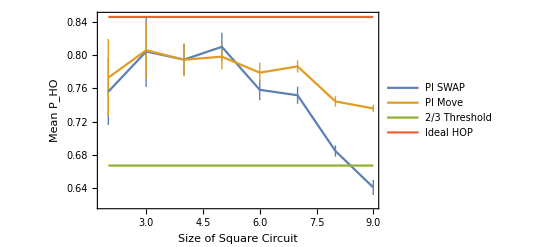

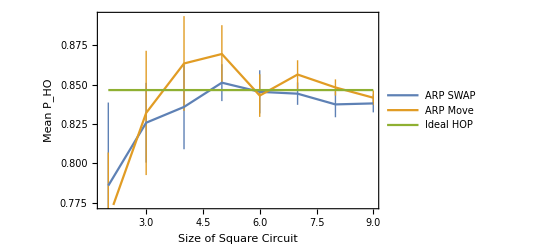

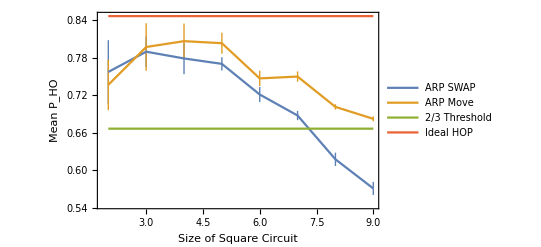

```mathematica
ErrorBar[DataSet_]:=Table[{DataSet[[i,1]],DataSet[[i,2]]±DataSet[[i,3]]},{i,1,Length[DataSet]}];

ListLinePlot[{ErrorBar[QVPIPropSWAP20[[All,2]]],ErrorBar[QVPIParMove20[[All,2]]],IdealHOP},AxesLabel->{HoldForm[Layer Depth],HoldForm[Heavy Output Generation Probability]},Frame->True,FrameLabel->{"Size of Square Circuit","Mean P_HO"},PlotLegends->{"PI SWAP","PI Move","Ideal HOP"}]
ListLinePlot[{ErrorBar[QVPIPropSWAP20[[All,1]]],ErrorBar[QVPIParMove20[[All,1]]],Thresh,IdealHOP},AxesLabel->{HoldForm[Layer Depth],HoldForm[Heavy Output Generation Probability]},Frame->True,FrameLabel->{"Size of Square Circuit","Mean P_HO"},PlotLegends->{"PI SWAP","PI Move","2/3 Threshold","Ideal HOP"}]
ListLinePlot[{ErrorBar[QVARPPropSWAP20[[All,2]]],ErrorBar[QVARPParMove20[[All,2]]],IdealHOP},AxesLabel->{HoldForm[Layer Depth],HoldForm[Heavy Output Generation Probability]},Frame->True,FrameLabel->{"Size of Square Circuit","Mean P_HO"},PlotLegends->{"ARP SWAP","ARP Move","Ideal HOP"}]
ListLinePlot[{ErrorBar[QVARPPropSWAP20[[All,1]]],ErrorBar[QVARPParMove20[[All,1]]],Thresh,IdealHOP},AxesLabel->{HoldForm[Layer Depth],HoldForm[Heavy Output Generation Probability]},Frame->True,FrameLabel->{"Size of Square Circuit","Mean P_HO"},PlotLegends->{"ARP SWAP","ARP Move","2/3 Threshold","Ideal HOP"}]
```

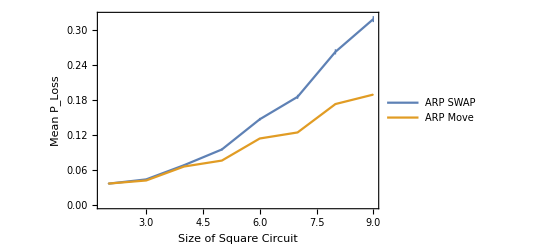

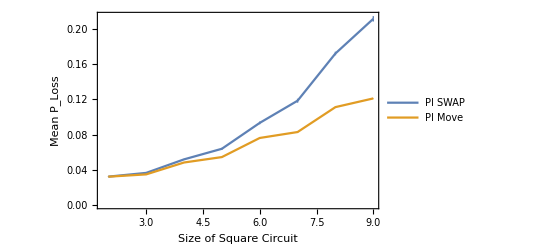

```mathematica
ListLinePlot[{ErrorBar[QVARPPropSWAP20[[All,3]]],ErrorBar[QVARPParMove20[[All,3]]]},AxesLabel->{HoldForm[Layer Depth],HoldForm[Heavy Output Generation Probability]},Frame->True,FrameLabel->{"Size of Square Circuit","Mean P_Loss"},PlotLegends->{"ARP SWAP","ARP Move"}]
ListLinePlot[{ErrorBar[QVPIPropSWAP20[[All,3]]],ErrorBar[QVPIParMove20[[All,3]]]},AxesLabel->{HoldForm[Layer Depth],HoldForm[Heavy Output Generation Probability]},Frame->True,FrameLabel->{"Size of Square Circuit","Mean P_Loss"},PlotLegends->{"PI SWAP","PI Move"}]
```